```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table_revreps.csv"}],"csv"];
predpreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/predpreymass_tablereps.csv"}],"csv"];
```

```mathematica
ppmrfitdata
```

{{Fit,FitLow,FitHigh},{3.61724,3.60882,3.62566},{0.225607,0.224237,0.226977}}

```mathematica
ppmrfitdata[[2,1]]
ppmrfitdata[[3,1]]
```

3.61724

0.225607

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-((α Y[M] (kRes (4 (bP[M]-λ[M]+μ[M])^2 (bP[M]+μ[M]+Y[M] ρ[M])+2 (5 bP[M]^2-5 bP[M] λ[M]+2 λ[M]^2+10 bP[M] μ[M]-5 λ[M] μ[M]+5 μ[M]^2+2 Y[M] (bP[M]+μ[M]) ρ[M]) σ[M]+(6 bP[M]-2 λ[M]+6 μ[M]+3 Y[M] ρ[M]) σ[M]^2)+2 bP[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 bP[M] λ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+4 bP[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] Y[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-Y[M] ρ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) (bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

Metabolic parameters for herbivore consumer

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

(*palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;*)
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)

(*OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;*)
(*OptPreyMass[Mp_]:=ⅇ^(pbeta/(2 pgamma)) *Mp;*)

(*OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;*)
(*OptPredMass[M_]:=ⅇ^(-pbeta/(2 pgamma)) *M;*)



(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

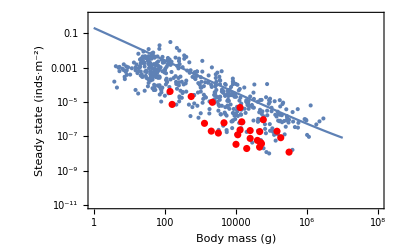

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.bP[M]->0,{M,1,10^7},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

```mathematica
PredDensity[Mp]
```

0.000862119 Mp^0.12

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify];
```

Two Predator reproduction rates : linear to the theoretical maximum and M-M with saturation derived from the theoretical maximum

Plot the Theoretical Maxima for herbivore consumers and predators relative to Damuth Data

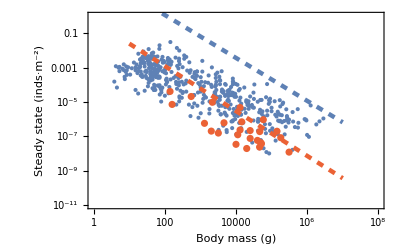

```mathematica
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxdensities.pdf"}],PredPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxdensities.pdf

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[w*predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

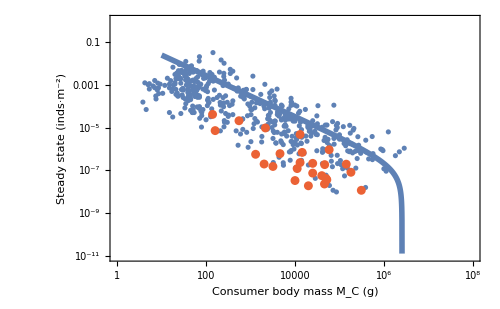

```mathematica
ConsInstabilityPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*Csol/.w->1,{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]}]
},ImageSize->500]
```

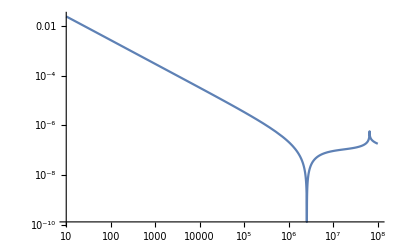

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2.54916×10^6

218815.

1.70864×10^7

335862.

```mathematica
LogLogPlot[Abs[(1/M)*Csol/.w->1],{M,10,10^8}]
PreySSMin=N[(FindMinimum[Abs[(1/M)*Csol/.w->1],M])];
MaxPreyMassSS=M/.PreySSMin[[2]]
MaxPredMassSS = OptPredMass[MaxPreyMassSS]

PreySSMinGen=N[(FindMinimum[Abs[(1/M)*Csol/.w->0.37],M])];
MaxPreyMassSSGen=M/.PreySSMinGen[[2]]
MaxPredMassSSGen = OptPredMass[MaxPreyMassSSGen]
```

```mathematica
SinclairHerbMass = {3000,2000,1200,800,450,400,170,120,50,18}*1000;
SinclairHerbPercMort = {0,0,0,5,23.3,73.4,86.8,100,100,100};
```

```mathematica
mnf=NonlinearModelFit[Transpose[{Log@SinclairHerbMass,SinclairHerbPercMort/100}],1-(1/(1 + Exp[-k*(x-mid)])),{{k,1},{mid,15}},x]
```

FittedModel[1-1/(1+ⅇ^(-18.7324 (-«19»+x)))]

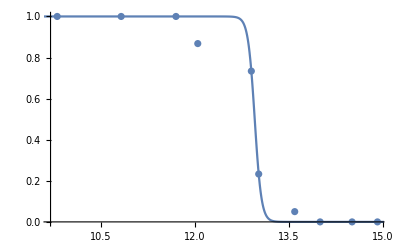

```mathematica
Show[{
ListPlot[Transpose[{Log@SinclairHerbMass,SinclairHerbPercMort/100}]],
Plot[mnf[x],{x,1,20}]
}]
```

```mathematica
mnf["ParameterTable"]
Exp[mnf["ParameterTableEntries"][[2,1]]]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 18.7324 | 3.21397 | 5.82844 | 0.00039226
mid | 12.9534 | 0.0100651 | 1286.96 | 1.48829×10^-22

422271.

```mathematica
mortalityfunc[M_]:=mnf[Log[M]]
mortalityfunc[M]
```

1-1/(1+ⅇ^(-18.7324 (-12.9534+Log[M])))

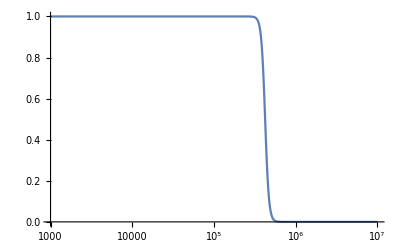

```mathematica
LogLinearPlot[mortalityfunc[M],{M,10^3,10^7}]
```

```mathematica
mnf
```

FittedModel[1-1/(1+ⅇ^(-18.7324 (-«19»+x)))]

```mathematica
MaxObsPreySizeGen=Flatten[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxobspreysize_gen.csv"}]],1]
```

{1.70864×10^7,0.37}

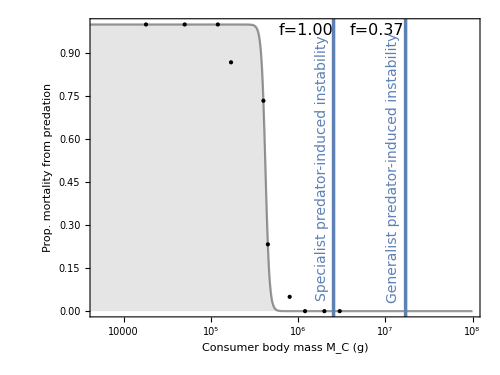

```mathematica
SinclairPlot = Show[{
ListLogLinearPlot[Transpose[{SinclairHerbMass,SinclairHerbPercMort/100}],Frame->True,PlotRange->{{5000,10^8},All},FrameLabel->{"Consumer body mass M_C (g)","Prop. mortality from predation"},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,PointSize[Large]}],
LogLinearPlot[mortalityfunc[M],{M,10^3,10^8},PlotStyle->{Black,Opacity[0.4]},Filling->Bottom,FillingStyle->{Black,Opacity[0.1]}],
Graphics[{Thickness[0.005],ColorData[97,1],Line[{{Log@MaxPreyMassSS,-10},{Log@MaxPreyMassSS,110}}]}],
Graphics[Text[Style["Specialist predator-induced instability",FontSize->14,ColorData[97,1]],{Log@MaxPreyMassSS*(1-0.02),0.50},Automatic,{0,100}]],
Graphics[Text[Style["f=1.00",FontSize->16,Black],{Log@MaxPreyMassSS*(1-0.05),0.98},Automatic]],
Graphics[Text[Style["f=0.37",FontSize->16,Black],{Log@(MaxObsPreySizeGen[[1]])*(1-0.045),0.98},Automatic]],
Graphics[{Thickness[0.005],ColorData[97,1],Line[{{Log@(MaxObsPreySizeGen[[1]]),-10},{Log@(MaxObsPreySizeGen[[1]]),110}}]}],
Graphics[Text[Style["Generalist predator-induced instability",FontSize->14,ColorData[97,1]],{Log@(MaxObsPreySizeGen[[1]])*(1-0.02),0.50},Automatic,{0,100}]]
},ImageSize->500,AspectRatio->3/4]
```

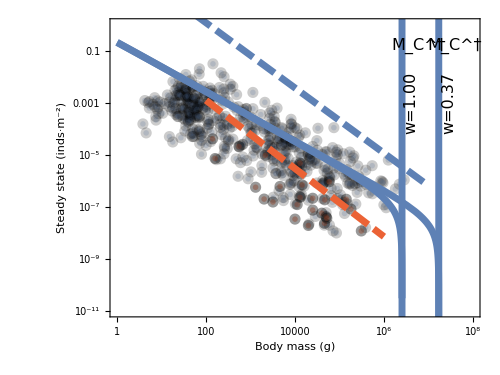

```mathematica
BodySizeLimitsPlot = Show[{
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.2],FaceForm[ColorData[97,1]],Disk[]}];
pstylepred=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.4],FaceForm[ColorData[97,4]],Disk[]}];
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},PlotMarkers->{pstyleherb,.03},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata(*,PlotStyle->ColorData[97,4],PlotMarkers->{"▲"}*),PlotMarkers->{pstylepred,.03}],
LogLogPlot[(1/M)*Csol/.w->1,{M,1,10^7},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/M)*Csol/.w->0.37,{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.01],Dashing[{Large,Small}],ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M],{M,10^2,10^6},Frame->True,PlotStyle->{Thickness[0.01],Dashing[{Large,Small}],ColorData[97,4]}],
Graphics[{Thickness[0.01],ColorData[97,1],Line[{{Log@MaxPreyMassSS,-100},{Log@MaxPreyMassSS,110}}]}],
Graphics[{Thickness[0.01],ColorData[97,1],Line[{{Log@MaxPreyMassSSGen,-100},{Log@MaxPreyMassSSGen,110}}]}],
(*Graphics[{Thickness[0.01],ColorData[97,4],Line[{{Log@MaxPredMassSS,-100},{Log@MaxPredMassSS,110}}]}],*)
Graphics[Text[Style["M_C^†",FontSize->16,Black],{Log@MaxPreyMassSS*(1+0.06),Log@0.155},Automatic]],
Graphics[Text[Style["M_C^†",FontSize->16,Black],{Log@MaxPreyMassSSGen*(1+0.05),Log@0.155},Automatic]],
Graphics[Text[Style["w=1.00",FontSize->16,Black],{Log@MaxPreyMassSS*(1+0.03),Log@0.001},Automatic,{0,1}]],
Graphics[Text[Style["w=0.37",FontSize->16,Black],{Log@MaxPreyMassSSGen*(1+0.03),Log@0.001},Automatic,{0,1}]](*,
Graphics[Text[Style["M_P^†",FontSize->16,Black],{Log@MaxPredMassSS*(1+0.06),Log@0.155},Automatic]]*)
(*,
Graphics[{ColorData[97,1],Opacity[0.6],Rectangle[{Log@(6*10^5),Log@(1*10^-10.8)},{Log@(1*10^7.9),Log@(1*10^-10.2)},RoundingRadius->0.3]}]*)
},ImageSize->500,AspectRatio->3/4]
```

```mathematica
nlm = NonlinearModelFit[predpreymassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000]
```

FittedModel[9668.36 x^0.210868]

```mathematica
lm =LinearModelFit[Log@(predpreymassdata*1000),x,x]
```

FittedModel[8.96656+0.225607 x]

```mathematica
lmparams=lm["BestFitParameters"]
```

{8.96656,0.225607}

```mathematica
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95]
```

{{9491.44,9845.28},{0.209497,0.212239}}

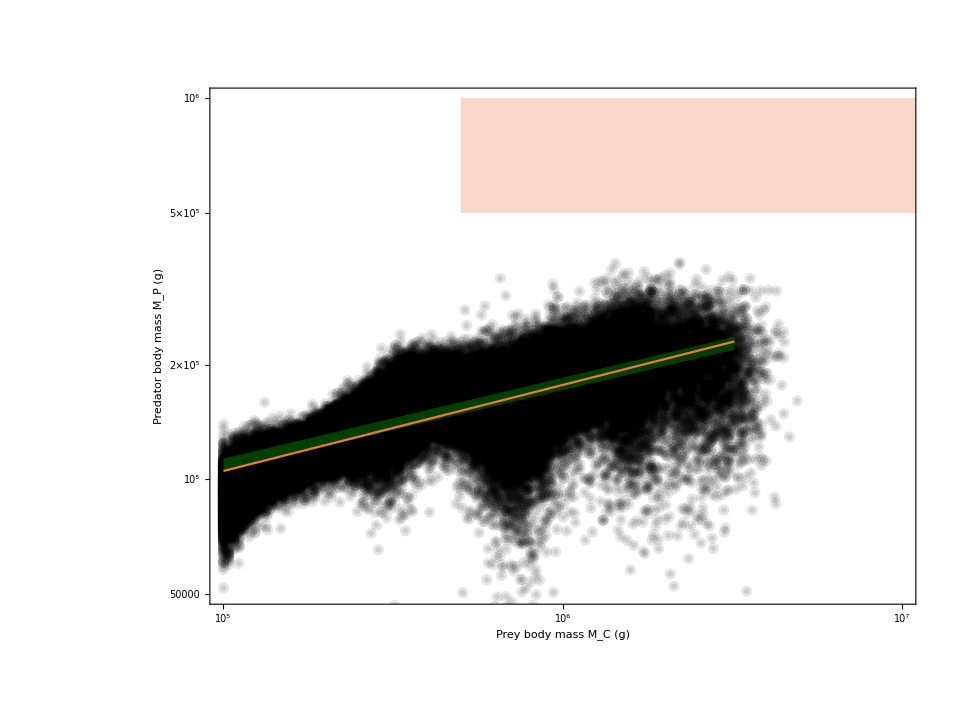

```mathematica
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[predpreymassdata*1000,Frame->True,FrameLabel->{"Prey body mass M_C (g)","Predator body mass M_P (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^5,1*10^7},{5*10^4,10^6}}],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,100000,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,100000,3200000},PlotStyle->ColorData[93,4]],
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]]
},ImageSize->500,AspectRatio->3/4]
```

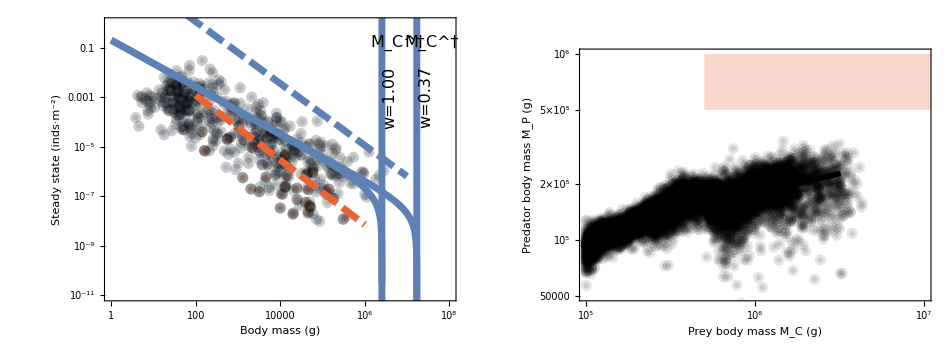

```mathematica
SteadyStateLimitsPlot=GraphicsRow[{BodySizeLimitsPlot,PPMRPlotNLM},ImageSize->950,Spacings->Scaled[0]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether_top.pdf"}],SteadyStateLimitsPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether_top.pdf

```mathematica
MaxConsumerSizePredPreyRatio=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio.csv"}]];
MaxConsumerSizePredPreyRatioSmall = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratiosmall.csv"}]];
MaxPredatorSizePredPreyRatio = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratio.csv"}]];
MaxPredatorSizePredPreyRatioSmall = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratiosmall.csv"}]];
SizePlotPositions =Intersection[Flatten[Position[MaxConsumerSizePredPreyRatio[[All,3]],_?(#>5*10^5&&#<1.74*10^7&)]],Flatten[Position[MaxPredatorSizePredPreyRatio[[All,3]],_?(#>5*10^5&&#<1.2*10^6 &)]]];
```

```mathematica
MegaMammalPlot=GraphicsRow[{
Show[{
ListDensityPlot[MaxConsumerSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_C^† (g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>1.5*10^6&&z<1.74*10^7]*),ColorFunction->ColorData["AtlanticColors"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350],
Show[{
ListDensityPlot[MaxPredatorSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_P^†(g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>500000&&z<1.2*10^6]*),ColorFunction->ColorData["SiennaTones"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350]
},ImageSize->950,Spacings->Scaled[-0.05]]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether_bottom.pdf"}],MegaMammalPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether_bottom.pdf

```mathematica
AllTogetherPlot = GraphicsColumn[{SteadyStateLimitsPlot,MegaMammalPlot},ImageSize->1000,Spacings->Scaled[-0.1]]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether.pdf"}],AllTogetherPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predation_alltogether.pdf

```mathematica
OptPredMass[1.74*10^7]
```

299979.

```mathematica
{Last[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],
First[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]]}
{First[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]],
Last[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]}
```

{1.72013×10^6,2.10257×10^6}

{500345.,1.18477×10^6}

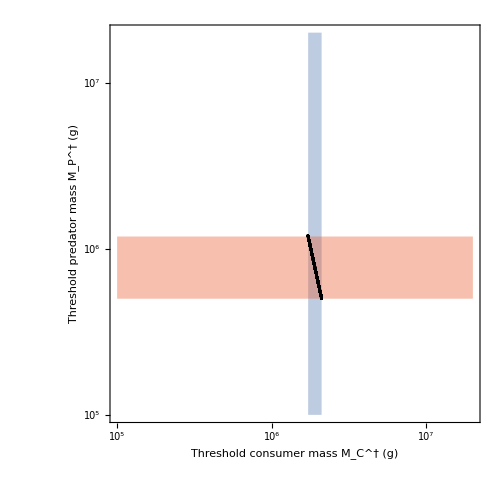

```mathematica
MegaMammalPlotSize=Show[{
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->Black,Frame->True,PlotRange->{{1*10^5,2*10^7},{1*10^5,2*10^7}},FrameLabel->{"Threshold consumer mass M_C^† (g)","Threshold predator mass M_P^† (g)"},LabelStyle->Directive[FontSize->16]],
Graphics[{ColorData[97,1],Opacity[0.4],Rectangle[{Log@First[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(1*10^5)},{Log@Last[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(2*10^7)}]}],
Graphics[{ColorData[97,4],Opacity[0.4],Rectangle[{Log@(1*10^5),Log@First[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]},{Log@(2*10^7),Log@Last[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]}]}],
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->Black]
},ImageSize->500,AspectRatio->1]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.pdf"}],MegaMammalPlotSize,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.pdf